# Problem Set 2

## Problem 1

p_(x,y)(k, l) = c(k^2+l^2)
k : {-1, 0, 1, 3}
l: {-1, 2, 3}
∑_k  ∑_l  p_(x,y) = 1
89c = 1
c = 1/89

### Checking my work

```mathematica
pxy = c(k^2 + l^2)
soln = Solve[Sum[Sum[pxy, {k, {-1, 0, 1, 3}}], {l, {-1, 2, 3}}] == 1, c]
pxy/.soln/.{k->3, l->3}
```

### Part II

p_(x,y)(k, l) = 1/89(k^2+l^2)
(y,x) | -1 | 0 | 1 | 3
-1 | 2/89 | 1/89 | 2/89 | 10/89
2 | 5/89 | 4/89 | 5/89 | 13/89
3 | 10/89 | 9/89 | 10/89 | 18/89

P(X≤1,Y>2) = 29/89

## Problem 2

```mathematica
pxy = Piecewise[{{24 x y, 0 < x < 1 && 0 <y < 1&& x + y < 1}, {0, True}}]
∫_(-∞)^∞ ∫_(-∞)^((1/2)-x) pxy ⅆy ⅆx
N[%]
```

Piecewise[{{24 x y, 0<x<1&&0<y<1&&x+y<1}, {0, True}}]

1/16

0.0625

## Problem 3

```mathematica
cxy = Piecewise[{{(1 - Exp[-x^2])(1-Exp[-y^2]), x≥0 && y ≥0}, {0, True}}]
pxy = D[D[cxy, x], y]
```

Piecewise[{{(1-ⅇ^(-x^2)) (1-ⅇ^(-y^2)), x≥0&&y≥0}, {0, True}}]

Piecewise[{{4 ⅇ^(-x^2) x y-4 ⅇ^(-x^2-y^2) (-1+ⅇ^(y^2)) x y, x≥0&&y≥0}, {0, True}}]

## Problem 4

```mathematica
cxy = Piecewise[{{1-Exp[-x]-Exp[-y]+Exp[-x-y], x≥0&&y≥0}, {0, True}}]
pxy = D[D[cxy, x], y]
(1-∫_3^∞ ∫_(-∞)^(y-3) pxy ⅆx ⅆy)//FullSimplify
N[%]
```

Piecewise[{{1-ⅇ^-x+ⅇ^(-x-y)-ⅇ^-y, x≥0&&y≥0}, {0, True}}]

Piecewise[{{ⅇ^-x-ⅇ^(-x-y) (-1+ⅇ^y), x≥0&&y≥0}, {0, True}}]

1-1/(2 ⅇ^3)

0.975106

## Problem 5

```mathematica
pxy = Piecewise[{{24 y (1-x-y), x > 0 && y > 0 && x+ y < 1}, {0, True}}]
```

Piecewise[{{24 (1-x-y) y, x>0&&y>0&&x+y<1}, {0, True}}]

```mathematica
mx =∫_(-∞)^∞ pxy ⅆx
```

Piecewise[{{12 (y-2 y^2+y^3), 0<y<1}, {0, True}}]

```mathematica
my =∫_(-∞)^∞ pxy ⅆy
```

Piecewise[{{-4 (-1+x)^3, 0<x<1}, {0, True}}]

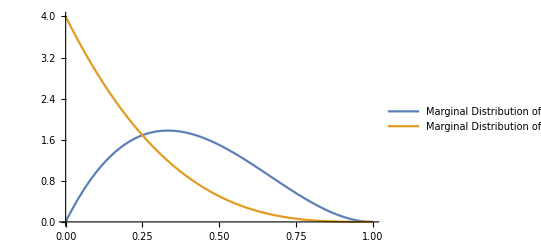

```mathematica
Plot[{
mx, 
my/.{x->y}}, 
{y, 0, 1}, 
PlotLegends->{"Marginal Distribution of y", "Marginal Distribution of x"}]
```

## Problem 6

```mathematica
MomentGeneratingFunction[ProbabilityDistribution[2 3^-x,{x,1,∞}],t]
firstMoment = D[(-(2 ⅇ^t)/(3 t-Log[27])), t]
secondMoment = D[((6 ⅇ^t)/(3 t-Log[27])^2-(2 ⅇ^t)/(3 t-Log[27])), t]
```

-(2 ⅇ^t)/(3 t-Log[27])

(6 ⅇ^t)/(3 t-Log[27])^2-(2 ⅇ^t)/(3 t-Log[27])

-(36 ⅇ^t)/(3 t-Log[27])^3+(12 ⅇ^t)/(3 t-Log[27])^2-(2 ⅇ^t)/(3 t-Log[27])

## Problem 7

Z = (X − 3)/4
Z = 1/4x - 3/4
M_x(t) = ⅇ^(3t+8 t^2)
M_z(t) = ⅇ^at M_x(bt)
M_z(t) = ⅇ^(t/4) M_x(3t/4) = ⅇ^(t/4) ⅇ^(3(3t/4)+8(3t/4)^2)= ⅇ^(1/2 t (5+9 t))
M'_z(t) = 1/2 ⅇ^(1/2 t (5+9 t)) (5+18 t)
M'_z(0) = 5/2
M''_z(t)=1/4 ⅇ^(1/2 t (5+9 t)) (61+36 t (5+9 t))

M''_z(0)=61/4

M''_z(0)-(M'_z(0))^2=61/4-(5/2)^2
M''_z(0)-(M'_z(0))^2=9
μ=5/2, σ=9

```mathematica
Exp[t/4] Exp[3(3t/4)+8(3t/4)^2]
D[%, t]
D[%, t]/.{t->0}//FullSimplify
%-((5/2)^2)
```

ⅇ^((5 t)/2+(9 t^2)/2)

ⅇ^((5 t)/2+(9 t^2)/2) (5/2+9 t)

61/4

9

## Problem 8

f_x(x) = 2 x ⅇ^(-x^2) 1_([0, ∞))(x)
Y = X^2
X = Y^(1/2)= g^-1(y)
(∂g^-1(y))/(∂y) = 1/2 y^(-1/2)
f_y(y) = f_x(y^(1/2)) 1/2 y^(-1/2) = 2 (y^(1/2)) ⅇ^((-y^(1/2))^2)1/2 ^(y-1/2)=  ⅇ^-y